```mathematica
Clear["Global`*"]
```

Variables to Adjust

```mathematica
Coordinates :={3,12,-24,35,-44,49,-48,41,-30,18,-8,2}
```

```mathematica
XMax := 19
```

```mathematica
XOffset:=-1
```

END of Variables to Adjust

```mathematica
SumOfBinomials[vector_,x_] := Sum[vector[[i+1]]*Binomial[x,i],{i,0,Length[vector]-1}]
```

```mathematica
p1:=Plot[SumOfBinomials[Coordinates,x+XOffset],{x,0,XMax+1},PlotRangePadding->1,GridLines->{{},Range[1,10000]}]
```

```mathematica
p2:=DiscretePlot[SumOfBinomials[Coordinates,x+XOffset],{x,1,XMax},AxesOrigin->{0,0}]
```

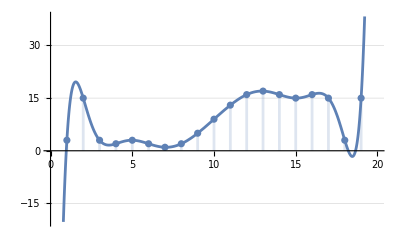

```mathematica
Show[p1,p2]
```

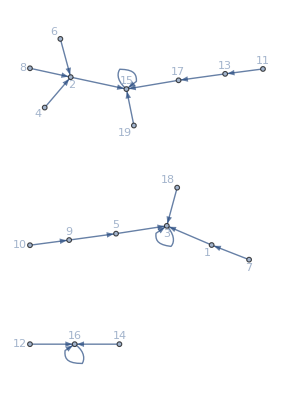

```mathematica
Show[Graph[Table[x->SumOfBinomials[Coordinates,x+XOffset],{x,1,XMax}],GraphLayout->"SpringElectricalEmbedding",VertexLabels->"Name"]]
```

```mathematica
Simplify[Expand[InterpolatingPolynomial[Table[SumOfBinomials[Coordinates,x+XOffset],{x,1,20}],x]]]
```

1/19958400(-6147187200+14001864480 x-11972517480 x^2+5442913916 x^3-1506249250 x^4+271401185 x^5-32919810 x^6+2714283 x^7-150150 x^8+5335 x^9-110 x^10+x^11)

```mathematica
B[Length[Coordinates]]=Coordinates[[-1]];B[x_]:=-B[x+1]+Coordinates[[x]];AdjustedCoordinates=Table[B[x],{x,1,Length[Coordinates]}]
```

{-308,311,-299,275,-240,196,-147,99,-58,28,-10,2}